# CO3 Monte Carlo Simulations

Defining a Random Walk and a Monte Carlo simulation:

```mathematica
RW[n_,p_]:=Block[{x=0},                                                        (*Random Walk of n steps, probability of going right p, starting at origin*)
Do[If[RandomReal[]≤p,x=x+1,x=x-1],n];
Return[x]]                                                                                                         (*List of values of x after every step*)
```

```mathematica
RW[100,0.5]
```

-14

### The value of x after one trial is not sufficient to make any conlcusions about the probability distribution. Therefore, we need to average over many trials to get a relatively smooth distribution curve which can be used to better model a probability distribution.

```mathematica
MC[t_,n_,p_]:=Table[RW[n,p],{i,t}]//Flatten                     (*Monte Carlo simulation with t trials/random walks*)
```

```mathematica
data1=MC[1000,100,0.5]
```

{-4,-14,-12,-16,4,-18,-6,-22,-4,-4,-8,-22,-2,4,4,-12,0,-14,4,6,6,-8,-6,-6,-10,-2,-6,10,-8,-8,8,-16,4,-12,18,-4,-2,0,14,-12,12,-26,8,16,-12,-2,10,2,-14,-6,10,6,10,-24,-6,14,-12,4,2,8,-16,-2,2,-8,-6,-4,6,12,6,-14,-10,-10,-8,-18,-16,-6,16,-4,-8,-6,4,-4,-8,-2,-22,-12,-4,-8,16,-22,-12,18,0,2,8,-14,-4,4,-2,12,0,10,14,16,0,4,-14,-12,-8,-2,-4,-14,8,18,-2,-14,6,2,0,12,8,18,0,-2,-12,16,8,-12,10,-14,-14,-8,8,18,-12,4,-22,-12,-12,2,-14,-4,6,4,0,10,4,-6,0,-8,2,12,4,-10,-6,2,16,-6,-10,8,16,-16,4,0,8,-6,8,4,16,4,12,0,-8,-2,10,-10,-4,0,-14,4,-18,-12,-18,-6,-2,2,2,16,-6,-8,20,-12,-10,8,-4,-24,-18,-14,18,12,14,4,18,-2,-4,8,8,-4,-4,-8,18,14,16,6,-18,-12,-10,2,-2,-2,-4,10,18,2,-8,-12,8,14,-2,8,12,0,2,16,6,0,0,-6,2,-10,-10,-4,-2,-12,0,16,-20,-4,2,-10,-14,8,-2,4,8,-16,-6,-18,-16,6,4,-2,12,10,14,-2,14,-4,-10,-6,2,0,4,6,14,-4,-2,8,14,4,14,-6,-2,6,0,6,-2,24,-2,-8,0,12,-2,14,-10,-14,12,6,4,16,6,-12,14,4,6,-16,-10,-8,-6,-4,4,4,4,-14,2,2,-12,-6,2,-12,10,-4,28,-12,2,8,-8,-8,0,4,-18,-16,-16,-12,0,-2,-2,-8,-16,-4,4,-14,2,-4,0,0,8,10,4,8,-6,-12,-4,-10,-22,-4,-8,4,0,4,-2,8,8,-10,0,2,12,-12,-22,14,0,0,2,-8,0,-4,0,-2,2,-2,-4,0,-16,-8,0,-8,6,2,2,0,10,2,-12,26,-12,4,6,-2,-8,6,0,-6,4,-6,-4,16,12,6,6,8,-10,-8,6,8,6,-4,-2,-6,-4,8,-2,-4,-18,-10,-2,0,2,6,10,-8,-12,18,-10,6,8,-2,4,0,2,-8,6,-28,-4,-4,-14,-2,0,18,2,0,8,-4,6,-8,-4,18,14,-10,10,12,-14,-10,4,-16,8,20,-6,4,6,24,0,2,2,4,-12,12,-2,8,-14,6,20,12,-2,-22,-4,-2,4,-6,-8,0,-2,-4,4,-4,10,10,8,2,-6,0,-6,2,8,-10,12,10,-4,-6,-8,-18,-2,-4,0,-6,16,2,10,-2,0,-6,-10,-6,-24,-18,4,0,-2,26,12,-16,-10,12,-14,-16,-2,-4,6,6,2,12,-2,4,-8,0,-4,2,-8,14,-4,-12,20,-4,0,-6,-16,-2,2,-12,-6,-20,10,-10,-20,-2,6,6,2,-2,-16,2,-2,-4,-18,-22,12,-10,0,0,-4,14,0,-2,-4,12,6,-8,10,-8,-2,18,-2,-4,-6,6,-14,-4,10,-14,18,-10,-22,-4,-4,-22,-14,-18,18,0,-18,6,-6,-4,0,-6,-4,8,6,-4,-14,-14,-14,-12,-4,-2,-6,-4,-4,4,-2,-6,2,-14,-2,-18,2,-18,-2,-16,-10,16,-12,-14,0,10,0,2,4,12,-20,10,6,4,-10,8,-2,-10,-8,4,12,-16,-8,-6,10,4,-4,-4,-12,-14,0,4,4,0,0,-2,6,-6,0,12,-12,10,4,-20,4,-8,10,4,0,-2,-14,-2,-32,-18,-8,14,-6,-10,-14,-6,-22,-2,2,8,-2,-10,-4,6,2,-8,-2,0,-2,2,0,-12,0,6,16,-4,10,2,2,-2,-8,-6,-10,2,-2,-4,2,6,-14,6,2,-4,18,-6,0,-8,26,4,28,-2,-2,-4,-4,22,18,10,10,-4,2,22,-4,-8,8,-10,10,-2,6,-8,0,16,6,-4,0,-4,2,-4,-6,10,-18,24,0,-16,-22,-4,-10,-4,0,-8,-8,-4,4,-2,-4,0,6,12,-6,14,22,18,0,4,-4,0,14,14,-12,-10,0,0,6,-2,-4,6,16,-8,0,6,10,-6,-2,4,26,20,12,0,18,-8,-4,-8,4,10,-22,-6,-4,-2,2,-8,-10,-16,-6,-10,-2,2,-16,4,2,4,12,-8,-10,-6,12,-6,-10,0,10,-18,0,-16,14,0,-20,-18,-16,-8,10,2,-24,-6,0,4,2,-2,16,-6,18,-2,16,2,8,10,16,-2,14,6,-12,-4,-2,-26,2,0,-8,16,6,-38,0,12,4,-12,-8,-6,-4,-2,0,-2,4,4,-12,2,-18,-14,6,2,-18,12,12,-2,-8,4,-2,-14,12,-2,8,10,0,-8,-6,-4,0,-18,8,-12,0,6,8,-4,0,0,-6,-6,-6,6,0,-2,16,-18,-10,2,-2,-16,-12,-8,-4,-10,-6,8,16,4,2,10,6,-12,14,-2,0,-2,4,4,4,-16,0,-10,-2,6,12,-18,-14,8,-4,-18,2,-26,2,-8,4,16,-4,-10,-12,14,4,-2,-8,2,-22,-2,12,-10,-8,6,26,0,14,20,2,8}

### We will not obtain the exact result for probability distribution by performing a Monte Carlo simulation but rather a numerically approximate distribution. The model for the probability distribution tends to the exact value as the number of trials ‘t’ tends to ∞.

```mathematica
Position[data1,1]
```

{{1},{3},{5},{7},{9},{11},{25},{53},{59},{65},{67},{69},{71},{73},{77},{79},{101},{103},{125},{127},{177},{179},{181},{183},{185},{189},{191},{193},{201},{203},{229},{301},6964,{99649},{99651},{99653},{99655},{99701},{99705},{99707},{99709},{99711},{99717},{99721},{99723},{99801},{99817},{99819},{99821},{99831},{99833},{99835},{99845},{99847},{99849},{99851},{99881},{99883},{99887},{99901},{99963},{99965},{99967},{99969},{99973}}
 |  |  |  |

Plotting histograms:

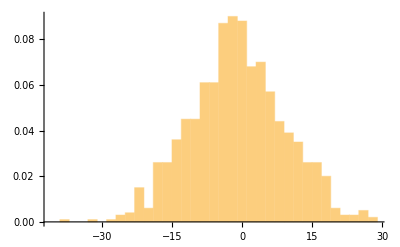

```mathematica
hist1=Histogram[data1,201,Probability,ChartLegends->"N=100"]
```

```mathematica
data2=MC[1000,500,0.5];
```

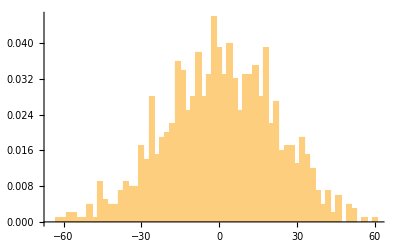

```mathematica
hist2=Histogram[data2,201,Probability,ChartLegends->"N=500"]
```

```mathematica
data22=MC[1000,250,0.5];
```

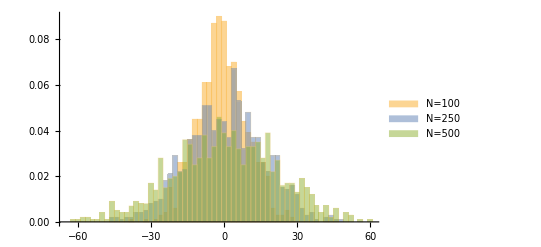

```mathematica
Histogram[{data1,data22,data2},201,"Probability",ChartLegends->{"N=100","N=250","N=500"}]
```

### As we can see from the above graph, as the value of N becomes larger, the histogram ( and the probability distribution) becomes shorter and wider. Therefore, the probability of getting the mean value (0) decreases and the probability of getting the extreme values increases. In essence, the distribution becomes broader and shorter as the total probability has to stay 1.

Monte Carlo simulations with N=16 and N=32 with p=1/2:

```mathematica
data3=MC[1000,16,0.5];
Freq3=Table[Length[Position[data3,i]],{i,-16,16}]                                                    (*Number of times each value of x occurs*)
```

{1,0,0,0,1,0,6,0,39,0,64,0,128,0,168,0,190,0,187,0,123,0,60,0,24,0,6,0,2,0,1,0,0}

```mathematica
xmp16=Position[Freq3,Max[Freq3]]-17                                                                     (*Corresponding value of x which has maximum frequency*)
```

{{0}}

```mathematica
data4=MC[1000,32,0.5];
Freq4=Table[Length[Position[data4,i]],{i,-32,32}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,4,0,13,0,17,0,28,0,52,0,66,0,124,0,119,0,162,0,122,0,105,0,82,0,62,0,24,0,17,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
xmp32=Position[Freq4,Max[Freq4]]-33
```

{{0}}

#### The most probable values of x for p=1/2 and N=16 and N=32 are 0 and 0 respectively.

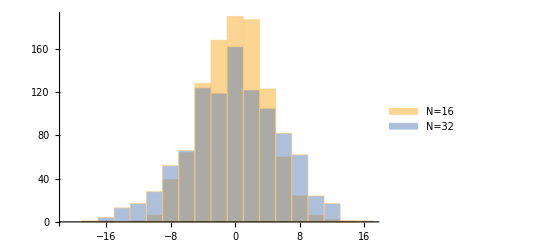

```mathematica
Histogram[{data3,data4},200,ChartLegends->{"N=16","N=32"}]
```

Finding width of distributions obtained with N = 100, 250 and 500 respectively:

```mathematica
Freq100=Table[Length[Position[data1,i]],{i,-100,100}]
Max[Freq100]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,3,3,7,9,15,19,26,36,52,64,85,99,120,139,164,204,285,348,448,557,696,786,962,1204,1545,1953,2431,2814,3268,3819,4517,5160,6025,6880,6974,7045,6171,5386,4715,4024,3526,2972,2669,2357,1997,1608,1299,1011,843,659,497,365,299,214,174,140,92,65,59,37,23,19,13,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

7045

```mathematica
x11=Position[Freq100,3268]-101
x12=Position[Freq100,3526]-101
```

{{-6}}

{{6}}

```mathematica
Freq250=Table[Length[Position[data22,i]],{i,-250,250}]
Max[Freq250]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,4,14,25,30,48,74,96,119,153,144,131,152,199,228,270,328,405,482,599,750,914,1071,1217,1319,1528,1825,2133,2448,2778,3070,3476,3802,4174,4629,5202,5758,6425,6998,7597,8143,8731,9479,10322,11187,11318,11410,10486,9611,8782,7984,7339,6779,6312,5763,5338,4882,4490,4038,3663,3272,2863,2435,2147,1816,1504,1292,1137,970,852,725,649,574,489,413,385,337,280,206,169,143,114,91,80,65,54,46,46,39,26,15,12,11,10,12,17,15,11,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

11410

```mathematica
x21=Position[Freq250,5758]-251
x22=Position[Freq250,5763]-251
```

{{-9}}

{{9}}

```mathematica
Freq500=Table[Length[Position[data2,i]],{i,-500,500}]
Max[Freq500]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,3,4,7,13,19,16,13,14,16,17,22,31,37,51,61,54,63,76,83,99,131,130,107,120,158,172,202,217,226,294,356,366,416,448,512,628,695,735,784,842,950,1100,1310,1489,1721,2004,2255,2398,2608,2970,3380,3667,3905,4131,4463,5042,5521,5829,6222,6716,7263,7653,8276,8987,9668,10231,10833,11341,11920,12608,13487,14451,15665,16861,16785,16997,16552,15761,14812,13845,13020,12293,11668,10879,10186,9379,8474,7755,7251,6842,6258,5557,5145,4844,4592,4238,3822,3460,3035,2632,2374,2163,1900,1726,1803,1741,1632,1544,1479,1322,1151,1047,976,869,815,753,674,583,455,369,350,324,296,267,250,254,226,185,158,127,129,116,85,56,35,22,19,28,39,30,29,34,37,51,61,49,25,13,13,11,6,8,6,1,1,1,1,1,3,9,9,4,2,1,2,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

16997

```mathematica
x31=Position[Freq500,8276]-501
x32=Position[Freq500,8474]-501
```

{{-12}}

{{12}}

### Width of the distribution with N=16: w_16=3-(-3)=6 Width of the distribution with N=32: w_32=4-(-4)=8 Similarly; w_100= 6-(-6)=12 w_250=9-(-9)=18 w_500=12-(-12)=24

Finding the relation between width w and no. of steps N:

```mathematica
datanw={{16,6},{32,8},{100,12},{250,18},{500,24}}
```

{{16,6},{32,8},{100,12},{250,18},{500,24}}

```mathematica
fit1=NonlinearModelFit[datanw,a*n^(1/b),{a,b},n]
fit2=NonlinearModelFit[datanw,a*√n,a,n]
```

FittedModel[1.88599 n^0.408652]

FittedModel[1.1253 √n]

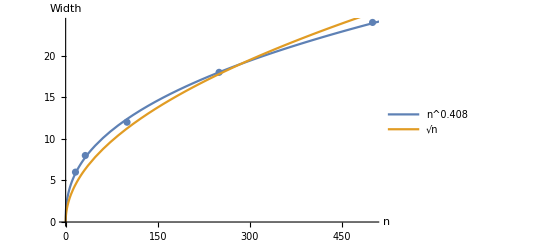

```mathematica
Show[ListPlot[datanw,AxesLabel->{"n","Width"}],Plot[{fit1[t],fit2[t]},{t,0,600},PlotLegends->{"n^0.408","√n"}]]
```

### From the above plot we can say that width nearly varies as square root of N. That is: w ∝ √N